自分の結果を書いたグラフ

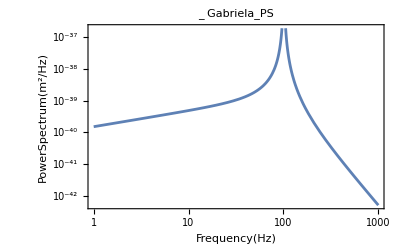

```mathematica
MyPS1=(4 kB T)/ω^2(ω s E0)/((M ω^2-s E0 k2 Cot[k2 L])^2)Abs[(χ ω)/((E0 s)^2+(χ ρ ω)^2)(α^2 T)/Cv(√(ω/(2χ))1/(Cosh[2kd L] -Cos[2 kd L]) ((Sin[2 kd L]+Sinh[2 kd L])((s E0)^2-(χ ρ ω)^2) ))] /.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};

MyPSg1=LogLogPlot[MyPS1,{f,1,1000},PlotLabel->Gabriela_PS_1,Frame->True,FrameLabel->{Frequency[Hz],PowerSpectrum[m^2/Hz]}]
```

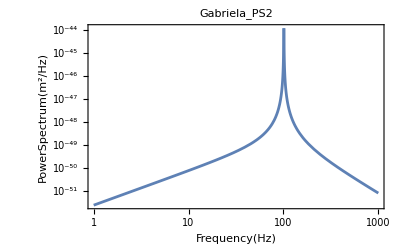

```mathematica
MyPS2=(4 kB T)/ω^2(ω s E0)/((M ω^2-s E0 k2 Cot[k2 L])^2)Abs[(χ ω)/((E0 s)^2+(χ ρ ω)^2)(α^2 T)/Cv(√(ω/(2χ))1/(Cosh[2kd L] -Cos[2 kd L]) ( - (Sin[2 kd L] - Sinh[2 kd L])2 χ ρ ω s E0)) ]/.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};

MyPSg2=LogLogPlot[MyPS2,{f,1,1000},PlotLabel->Gabriela_PS2,Frame->True,FrameLabel->{Frequency[Hz],PowerSpectrum[m^2/Hz]}]
```

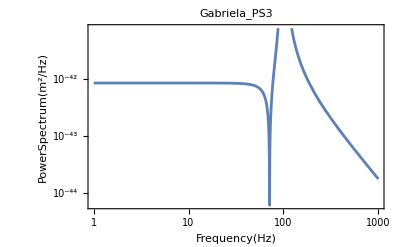

```mathematica
MyPS3=(4 kB T)/ω^2(ω s E0)/((M ω^2-s E0 k2 Cot[k2 L])^2)Abs[(χ ω)/((E0 s)^2+(χ ρ ω)^2)(α^2 T)/Cv(-(k2 Cot[k2 L]-2(M ω^2)/(s E0))((s E0)^2-(χ ρ ω)^2)) ]/.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};

MyPSg3=LogLogPlot[MyPS3,{f,1,1000},PlotLabel->Gabriela_PS3,Frame->True,FrameLabel->{Frequency[Hz],PowerSpectrum[m^2/Hz]}]
```

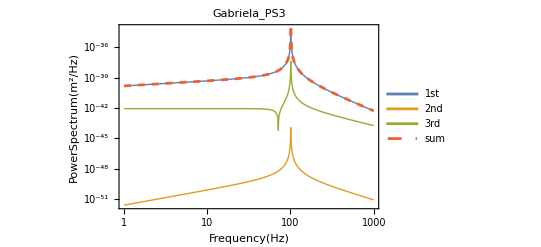

```mathematica
MyPSg123=LogLogPlot[{MyPS1,MyPS2,MyPS3,MyPS1+MyPS2+MyPS3},{f,1,1000},PlotLabel->Gabriela_PS3,Frame->True,FrameLabel->{Frequency[Hz],PowerSpectrum[m^2/Hz]},PlotLegends->Placed[{"1st","2nd","3rd","sum"},{0.3,0.33}],PlotStyle->{Thick,Thick,Thick,Dashed},GridLinesStyle->LightGray,GridLines->Full]
```

2.10852×10^-21 √((-((6.46814×10^11-4.04842×10^-13 f^2) (-0.000559596 f^2+0.000626657 √(f^2) Cot[0.00021933 √(f^2)]))+(498.183 √f (-1.02344 f (Sin[348.703 √f]-Sinh[348.703 √f])+(6.46814×10^11-4.04842×10^-13 f^2) (Sin[348.703 √f]+Sinh[348.703 √f])))/(-Cos[348.703 √f]+Cosh[348.703 √f]))/((6.46814×10^11+4.04842×10^-13 f^2) (225.027 f^2-503.988 √(f^2) Cot[0.00021933 √(f^2)])^2))

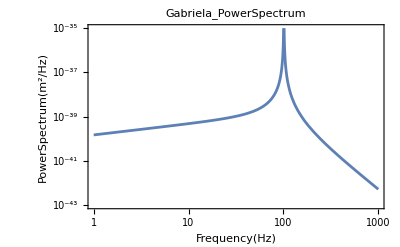

```mathematica
MyPS=(4 kB T)/ω^2(ω s E0)/((M ω^2-s E0 k2 Cot[k2 L])^2)(χ ω)/((E0 s)^2+(χ ρ ω)^2)(α^2 T)/Cv(√(ω/(2χ))1/(Cosh[2kd L] -Cos[2 kd L]) ((Sin[2 kd L]+Sinh[2 kd L])((s E0)^2-(χ ρ ω)^2) - (Sin[2 kd L] - Sinh[2 kd L])2 χ ρ ω s E0)-(k2 Cot[k2 L]-2(M ω^2)/(s E0))((s E0)^2-(χ ρ ω)^2)) /.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};
GabSensi=√MyPS /200/3000

MyPSg=LogLogPlot[MyPS,{f,1,1000},PlotRange->{10^-43,10^-35},PlotLabel->Gabriela_PowerSpectrum,Frame->True,FrameLabel->{Frequency[Hz],PowerSpectrum[m^2/Hz]}] (*my result*)
(*Sensitivity*)
```

Langevin approach

1.85195×10^-14 √((-Sin[348.703 √f]+Sinh[348.703 √f])/(√f (804248.-78.7594 f^2)^2 (-Cos[348.703 √f]+Cosh[348.703 √f])))

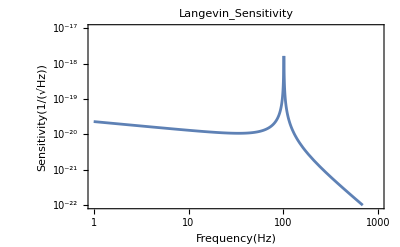

```mathematica
LangevinPS=((s E0)/(s E0-M ω^2 L))^2(2 kB T^2 α^2 L^3)/κ 1/(kd L)(Sinh[2 kd L]-Sin[2 kd L])/(Cosh[2 kd L]-Cos[2 kd L])/.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};
LangevinSensi=Sqrt[LangevinPS] / 200 / 3000
LangevinSensiG=LogLogPlot[LangevinSensi,{f,1,1000},PlotRange->{{1,1000},{10^-22,10^-17}},PlotLabel->Langevin_Sensitivity,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]
```

Langevin & Admittance

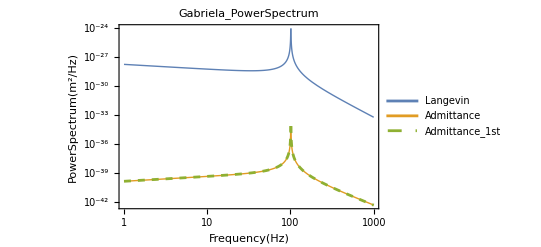

```mathematica
LogLogPlot[{LangevinPS,MyPS,MyPS1},{f,1,1000},PlotLabel->Gabriela_PowerSpectrum,Frame->True,FrameLabel->{Frequency[Hz],PowerSpectrum[m^2/Hz]},PlotLegends->Placed[{"Langevin","Admittance","Admittance_1st"},{0.3,0.4}],PlotStyle->{Thick,Thick,Dashed}]
```